# STATISTIKA PROMETNIH NESREČ

Pri predmetu Računalniška orodja v matematiki sem si za seminarsko nalogo ob koncu semestra izbrala temo Statistika prometnih nesreč. Zbrala bom statistiko o prometnih nesrečah in jo primerjala s statistiko prejšnjih let, ter na koncu prikazala rezultate. Prikazala bom tudi število smrtnih žrtev in število poškodovancev glede na leto in primerjala med leti.  Izračunama bom tudi kakšno aritmetično sredino in modus, ter geometrijsko sredino. Zelo pomembne so tudi posledice prometnih nesreč ter vzroki, zato bom tudi ta del posebej omenila. 

Za začetek, kaj sploh prometna nesreča je? Vsi nekako vemo, kaj pomeni in si, na podlagi lastnih videnj in izkušenj, ustvarimo določeno sliko. Po definiciji na wikipediji je prometna nesreča nesreča na javni cesti in nekategorizirani cesti, ki je dana v uporabo za cestni promet, v kateri je bilo udeleženo vsaj eno premikajoče se vozilo in je v njej ena ali več oseb umrlo, bilo telesno poškodovanih ali je nastala gmotna škoda. Seveda označujemo besedno zvezo prometna nesreča tudi za še več pojmov, ki pa niso povezani le z avtomobili in stanjem na cestah. V moji seminrski nalogi se bom osredotočila le na prometne nesreče na cestah in razna razmerja, povezana s tem.

PROMETNE NESREČE PRIKAZANE OD LETA 2014 DO 2018

# ŠTEVILO PROMETNIH NESREČ

```mathematica
prometnenesreče2014=18251
prometnenesreče2015=17943
prometnenesreče2016=17931
prometnenesreče2017=17584
prometnenesreče2018=18098
```

18251

17943

17931

17584

18098

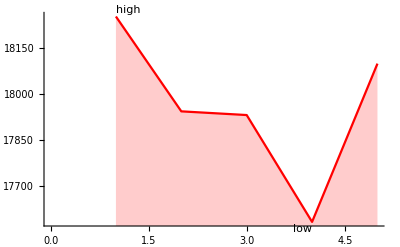

```mathematica
ListLinePlot[{prometnenesreče2014, prometnenesreče2015, prometnenesreče2016, prometnenesreče2017, prometnenesreče2018}, Filling->Axis,PlotStyle->RGBColor[1,0,0],PlotLabels->{Placed[{"high","low"},{Above, Below}]}]
```

V zgornjem grafu sem prikazala število prometnih nesreč od leta 2014 do 2018. Leta 2014 je bilo 18251 prometnih nesreč, leta 2015 le bilo 17943 nesreč. Leta 2016 je bilo 17931 prometnih nesreč, leta 2017 je bilo, kot lahko vidimo na grafu, najmanj prometnih nesreč. Bilo jih je 17584.Leta 2018 pa je nilo 18098 nesreč. Največ prometnih nesreč je bilo leta 2014, kar 18251. Na grafu hitro opazimo tudi najvišjo vrednost in najnižjo vrednost prometnih nesreč.

```mathematica
Mean[{prometnenesreče2014,prometnenesreče2015,prometnenesreče2016,prometnenesreče2017,prometnenesreče2018}]
```

89807/5

Izračunala sem povprečno vrednost vseh prometnih nesreč od leta 2014 do leta 2018. Ta znaša 44903,5. Povprečno se torje na leto zgodi toliko prometnih nesreč (izračunano na podlagi do sedanjih nesreč).

# ŠTEVILO SMRTNIH IZIDOV

```mathematica
smrtniizidi2014=108
smrtniizidi2015=120
smrtniizidi2016=130
smrtniizidi2017=104
smrtniizidi2018=91
```

108

120

130

104

91

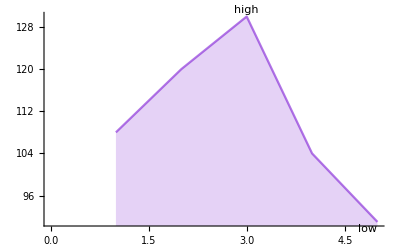

```mathematica
ListLinePlot[{smrtniizidi2014,smrtniizidi2015, smrtniizidi2016, smrtniizidi2017, smrtniizidi2018}, Filling->Axis,PlotStyle->RGBColor[0.5,0.12,0.84,0.61],PlotLabels->{Placed[{"high","low"},{Above, Below}]}]
```

V vijolično obarvanem grafu prikazujem število smrtnih izidov v prometnih nesrečah. To pomeni, da je na primer v letu 2017 med vsemi 17584 prometnimi nesrečami umrlo 104 ljudi in tako naprej za vsako leto posebej. V preteklem letu je skupaj umrlo 81 ljudi, kar je daleč najmanj v zadnjih petih letih. V primerjavi z letom 2017 je to -12, 5 % manj smrtnih žrtev , v primerjavi z letom 2014 pa je kar -15, 7 %.

```mathematica
Median[{smrtniizidi2014,smrtniizidi2015,smrtniizidi2016,smrtniizidi2017,smrtniizidi2018}]
```

108

Glede na podatke o smrtnih izidih sem izračunala Mediano. Ta znaša 108.

# ŠTEVILO POŠKODOVANIH

```mathematica
poškodovani2014=8220
poškodovani2015=8710
poškodovani2016=8456
poškodovani2017=7901
poškodovani2018=7613
```

8220

8710

8456

7901

7613

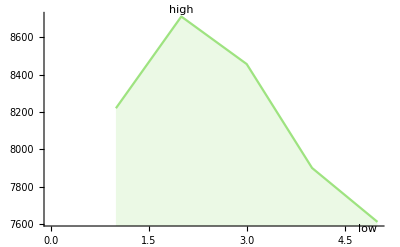

```mathematica
ListLinePlot[{poškodovani2014,poškodovani2015,poškodovani2016,poškodovani2017,poškodovani2018}, Filling->Axis,PlotStyle->RGBColor[0.62,0.89,0.5],PlotLabels->{Placed[{"high","low"},{Above, Below}]}]
```

Zeleni graf prikazuje število poškodovanih v prometnih nesrečah. Leta 2014 je bilo poškodovancev 8220, leto kasneje 8710. Leta 2016 jih je bilo 8456, nato 7901 in lansko leto najmanj, 7613. Razbrano glede na graf je leta 2015 bilo najvišjo število poškodovanih, najnižje leta 2018. 

V letu 2018 je bilo manj poškodovanih za kar -7, 4 % kot v letu 2014, ter -3, 6 % kot v letu 2017. 

Glede na celotno do sedanjo statistiko lahko ugotovimo, da je kljub visokemu številu prometnih nesreč v letu 2018 bilo nekoliko manjše število smrtnih izidov ter poškodovanih.

```mathematica
GeometricMean[{poškodovani2014,poškodovani2015,poškodovani2016,poškodovani2017,poškodovani2018}]
```

2 5^(2/5) 45520062684684042^(1/5)

Z zgornjo funkcijo sem izračunala geometrijsko sredino vrednosti med danimi podatki o poškodovanih.

# VZROKI PROMETNIH NESREČ

Za vzroke prometnih nesreč navajamo veliko različnih dejanj. Poznamo dejavnike, na katere ne moremo vplivati. To so naravni pojavi in so lahko dejavnost vremena, potresov, raznih sunkov, zemeljskih in snežnih plazov, poledica cestišča itd. Na žalost pa na prometne nesreče vplivajo tudi drugi dejavniki, ki so odraz posameznika. Voznik je lahko povzročitelj nesreče v raznih stanjih. Ena izmed teh je alkoholiziranost, ali ostale prepoedane substance, velikokrat je razlog tudi v neprilagojeni hitrosti, kjer voznik lažje zgubi kontrolo nad vozilom in tako povzroči nesrečo. Velikokrat na izid vplivajo tudi izkušnje, saj imajo mladostniki, ki so komaj naredili izpit, veliko manj izkušenj na cesti in v takih primerah mnogokrat ne reagirajo pravilno. Vzrokov za nastanek prometnih nesreč je veliko, dosti pa lahko storimo tudi sami, da poskušamo to preprečiti. 

Odstotek pozitivnih strokovnih pregledov na alkohol povzročiteljev prometnih nesreč s smrtnim izidom se v obdobju 2011 do 2017 giblje med 31 in 45 odstotki, leta 2017 pa znaša 37 odstotkov. 
Z aritmetično sredino bom izračunala, koliko je povprečno odstotkov pozitivnih pregledov na alkohol med leti 2011 in 2017.

```mathematica
odstotek1=31
odstotek2 =45
```

31

45

```mathematica
Mean[{odstotek1,odstotek2}]
```

38

# POSLEDICE PROMETNIH NESREČ

Posledice prometnih nesreč so lahko morfološke/anatomske (trajne deformacije, manjkajoči deli telesa), funkcionalne (nevrološki izpadi, omejena gibljivost, moteno delovanje organov) in časovne (odsotnost od družine/dela, nemožnost ukvarjanja z ostalimi dejavnostmi). Kot ena najhujših oblik posledic pa so psihološke posledice (ob zigubi bližnjih ali kot povzročitelj nesreče).

```mathematica
hudatelesnapoškodba2014=826
hudatelesnapoškodba2015=932
hudatelesnapoškodba2016=850
hudatelesnapoškodba2017=851
```

826

932

850

851

```mathematica
lažjatelesnapoškodba2014=7394
lažjatelesnapoškodba2015=7778
lažjatelesnapoškodba2016=7606
lažjatelesnapoškodba2017=7050
```

7394

7778

7606

7050

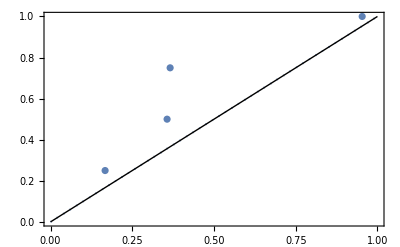

```mathematica
ProbabilityPlot[{hudatelesnapoškodba2014,hudatelesnapoškodba2015,hudatelesnapoškodba2016,hudatelesnapoškodba2017}]
```

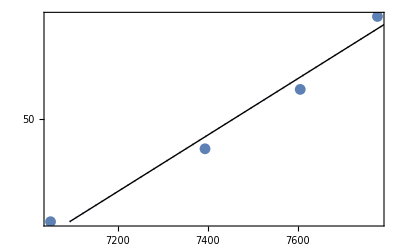

```mathematica
ProbabilityScalePlot[{lažjatelesnapoškodba2014,lažjatelesnapoškodba2015,lažjatelesnapoškodba2016,lažjatelesnapoškodba2017}]
```

Pikice na grafih prikazujejo vrendost hudih in lažjih poškodb med nesrečami. Največ hujših poškodb je bilo leta 2015, najmanj lažjih telesnih poškodb pa je bilo leta 2014.

# POVZROČITELJI PROMETNIH NESREČ V LETU 2017

Povzročitelji v letu 2017 so bili predvsem vozniki osebnih in enoslednih avtomobilov, pešci, kolesarji, vozniki tovornih vozil in ostali. Posledice povzročiteljev voznikov osebnih avtomobilov so bile s smrtnimi izidi, lažjimi in hujimi telesnimi poškodbami.
  
  VOZNIKI OSEBNIH AVTOMOBILOV :

```mathematica
smrt=65
hudatelpoškodba=433
lažjatelposškodba=5140
```

65

433

5140

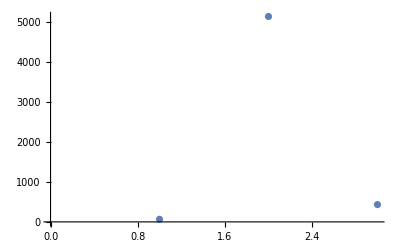

```mathematica
ListPlot[{smrt,lažjatelposškodba,hudatelpoškodba}]
```

VOZNIKI ENOSLEDNIH MOTORNIH VOZIL:

```mathematica
ClearAll
```

ClearAll

```mathematica
smrtmotornihvozil=22
hudatelpoš=148
lažjatelpoš=407
```

22

148

407

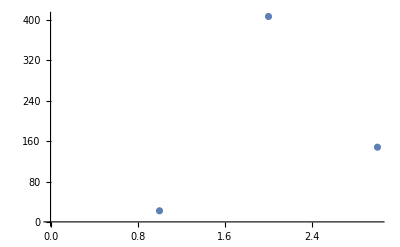

```mathematica
ListPlot[{smrtmotornihvozil,lažjatelpoš,hudatelpoš}]
```

PEŠCI:

```mathematica
smrtpešcev=1
lažjepoškodovani=80
hujepoškodovani=25
```

1

80

25

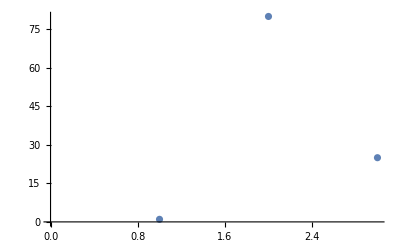

```mathematica
ListPlot[{smrtpešcev,lažjepoškodovani,hujepoškodovani}]
```

KOLESARJI :

```mathematica
smrtkolesarjev=4
lažjepoškolesarji=478
hujepoškolesarji=131
```

4

478

131

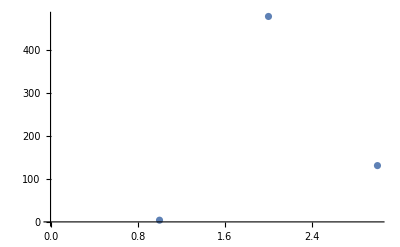

```mathematica
ListPlot[{smrtkolesarjev,lažjepoškolesarji,hujepoškolesarji}]
```

# VIRI

```mathematica
Hyperlink["https://www.ncbi.nlm.nih.gov/pmc/articles/PMC4347895/"]
```

https://www.ncbi.nlm.nih.gov/pmc/articles/PMC4347895/

```mathematica
Hyperlink["http://www.mzi.gov.si/fileadmin/mzi.gov.si/pageuploads/DP_varnost_cp/Elaborat.pdf"]
```

http://www.mzi.gov.si/fileadmin/mzi.gov.si/pageuploads/DP_varnost_cp/Elaborat.pdf

```mathematica
Hyperlink["https://www.avp-rs.si/wp-content/uploads/2012/02/Analiza-in-pregled-stanja-varnosti-cestnega-prometa_SEPTEMBER_20151.pdf"]
```

https://www.avp-rs.si/wp-content/uploads/2012/02/Analiza-in-pregled-stanja-varnosti-cestnega-prometa_SEPTEMBER_20151.pdf